```mathematica
NS["study_overlearning_conj3"]
```

```mathematica
(* coords transfs to plot the two-distribution space *)
```

```mathematica
norma:=If[Total[#]>0,(#/Total[#]),Null]&;
offset={1/20,0};
trmatrix2=T[{{0,1},{Sqrt[3]/2,1/2}, {0,0}}];
trmatrix=T[{{0,1},{-Sqrt[3]/2,1/2}, {0,0}}];
proj[p_]:=trmatrix.p-offset;
proj2[p_]:=trmatrix2.p+offset;

plotfreqs2[freqs_]:=Block[{nfreqs=norma@Flatten@freqs},If[nfreqs===Null,Nothing,Graphics[{{PointSize@Large,red,Point[proj@nfreqs]}}]]];
plotcfreqs2[freqs_]:=Block[{nfreqs=norma@Flatten@freqs},If[nfreqs===Null,Nothing,Graphics[{{Thick,red,Circle[proj@nfreqs,0.02]}}]]];

plotfreqs[freqs_]:=Block[{nfreqs=norma@Flatten@freqs},If[nfreqs===Null,Nothing,Graphics[{{PointSize@Large,purpleblue,Point[proj2@nfreqs]}}]]];
plotcfreqs[freqs_]:=Block[{nfreqs=norma@Flatten@freqs},If[nfreqs===Null,Nothing,Graphics[{{Thick,purpleblue,Circle[proj2@nfreqs,0.02]}}]]];
sp1={Black,Thin,Line[(-offset+#)&/@T[trmatrix][[{1,2,3,1}]]]};
sp2={Black,Thin,Line[(offset+#)&/@T[trmatrix2][[{1,2,3,1}]]]};
```

```mathematica
(* parametric model *)
ls=Range[0,2];g[s_]:=1+KroneckerDelta[s,1];
SetAttributes[g,Listable];gls=g[ls];
expsum[t_]=Table[g[s]*Exp[t*s],{s,ls}];
z[t_]=Total@expsum[t];
prob[t_]=FullSimplify[expsum[t]/z[t]]
```

{1/((1+ⅇ^t)^2),1/(1+Cosh[t]),ⅇ^(2 t)/((1+ⅇ^t)^2)}

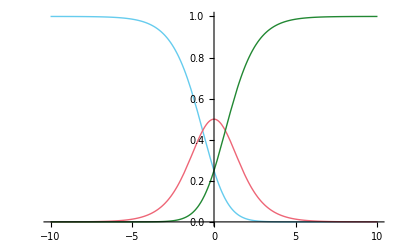

```mathematica
Plot[Evaluate@prob[t],{t,-10,10}]
```

```mathematica
Simplify[z[-t]/z[t]]
```

ⅇ^(-2 t)

```mathematica
v
```

```mathematica
assu=(0<k<2*n) (*for ls={0,1,2} *);
(* -n<k<n (*for ls={-1,0,1}*); *)
assu2=(Element[k,Integers]&&Element[n,Integers]);
uconj[t_,k_,n_]=Exp[k*t]/z[t]^n;
qq[k_,n_]=Assuming[assu,Simplify@Integrate[uconj[t,k,n],{t,-Infinity,Infinity}]]
```

Hypergeometric2F1[k,2 n,1+k,-1]/k-Hypergeometric2F1[2 n,-k+2 n,1-k+2 n,-1]/(k-2 n)

```mathematica
assu=(0<k<2*n) (*for ls={0,1,2} *);
(* -n<k<n (*for ls={-1,0,1}*); *)
assu2=(Element[k,Integers]&&Element[n,Integers]);
uconj[t_,k_,n_]=Exp[k*t]/z[t]^n;
qq[k_,n_]=Assuming[assu&&assu2,Simplify@Re@Integrate[uconj[t,k,n],{t,-Infinity,Infinity}]]
```

Re[Hypergeometric2F1[k,2 n,1+k,-1]/k-Hypergeometric2F1[2 n,-k+2 n,1-k+2 n,-1]/(k-2 n)]

```mathematica
qq[30.2,100.2]//N
```

6.32426×10^-38

```mathematica
Hypergeometric2F1[10.2,20.1,15.3,-4]
```

2.68951×10^-9

```mathematica
testf[k_,n_]:=Hypergeometric2F1[k,2 n,1+k,-1];
```

```mathematica
testf[20.1,100.1]
```

5.42796×10^-28

```mathematica
1.9218747677376263*^-61
```

1.92187×10^-61

```mathematica
conj[t_,k_,n_]=Assuming[assu,FullSimplify@(uconj[t,k,n]/qq[k,n])]
```

(ⅇ^(k t) ((1+ⅇ^t)^2)^-n)/Re[(-1)^(k-2 n) Beta[-1,-k+2 n,1-2 n]+Gamma[k] Hypergeometric2F1Regularized[k,2 n,1+k,-1]]

```mathematica
Hypergeometric2F1Regularized[0.1,2*0.1,0.1+1,-1]//N
```

1.03614

```mathematica
cprob[s_,k_,n_]=Assuming[assu&&-1<s<1,FS[g[s]*qq[k+s,n+1]/qq[k,n]]];
SetAttributes[cprob,Listable]
```

```mathematica
maxt[k_,n_]=(t/.Flatten@Assuming[assu,FS@Solve[D[uconj[t,k,n],t]==0,t,Reals]])
```

Log[-k/(k-2 n)]

```mathematica
mprob[k_,n_]=Assuming[assu,FullSimplify@prob[maxt[k,n]]]
```

{(k-2 n)^2/(4 n^2),-(k (k-2 n))/(2 n^2),k^2/(4 n^2)}

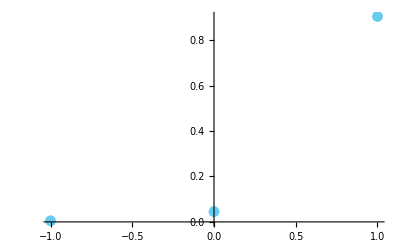

```mathematica
ListPlot[cprob[ls,19,10],DataRange->{-1,1},PlotRange->{0,All}]
```

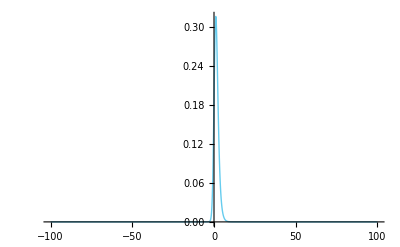

```mathematica
Plot[conj[t,3,2],{t,-100,100},PlotRange->All]
```

```mathematica
gendata[rfreqs_,ndata_,seed_:666]:=Block[{hi={1/2,1/2},idata,odata},
SeedRandom[seed];
idata=RandomChoice[hi->Range[2],ndata];
odata=Table[RandomChoice[rfreqs[[d]]->ls],{d,idata}];
{idata,odata}];
```

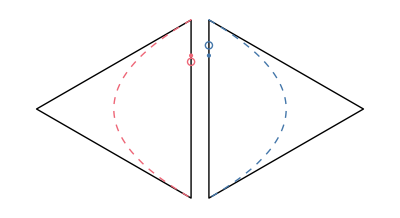

```mathematica
rfreqs={{4/5*12/12,0/12,1/5*12/12},
{4/5*12/12,0/12,1/5*12/12}};

(*rfreqs={prob[3],prob[3]};*)
samples=100;
{idata,odata}=gendata[rfreqs,samples];

dfreqs=Table[norma[Count[Pick[odata,idata,i],#]&/@ls],{i,2}];

ppplot1=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,red,Dashed}];
ppplot2=ParametricPlot[proj2@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue,Dashed}];
ddoms={Graphics[{sp1,sp2}],ppplot1,ppplot2};
Show[{ddoms,plotfreqs@rfreqs[[1]],plotcfreqs@dfreqs[[1]],plotfreqs2@rfreqs[[2]],plotcfreqs2@dfreqs[[2]]},PlotRange->All]
```

```mathematica
idata={2,2,1,1,1};odata={0,0,0,0,0};
```

```mathematica
ProgressIndicator[Dynamic[i],{0,samples}]
```

```mathematica
calcprob[alldata_,kk0_,nn0_]:=Block[{idata=alldata[[1]],sdata=alldata[[2]]+1,samples=Length[alldata[[1]]],qq0=qq[kk0,nn0],gls=g[ls],
probh,mlprobh,oprob,omlprob,logev,kkl,nnl,freqs=Table[0,{2},{3}],oldqq},
probh=Table[Null,{samples}];
mlprobh=Table[Null,{samples}];
oprob=Table[Null,{samples}];
omlprob=Table[Null,{samples}];
logev=Table[Null,{samples}];
kkl=Table[Null,{samples}];
nnl=Table[Null,{samples}];

oldqq=qq0;
Do[(*Print[i];Print[freqs];*)
kkl[[i]]=kk0+(ls.freqs[[1]])-(ls.freqs[[2]])+2*Total[freqs[[2]]];
nnl[[i]]=nn0+i-1;
newqq=Times@@(gls^Total[freqs])*
{gls*qq[kkl[[i]]+ls,nnl[[i]]+1],
gls*qq[kkl[[i]]+(2-ls),nnl[[i]]+1]};
(*Print[{i,integral//MF}];*)

probh[[i]]=newqq/oldqq;
mlprobh[[i]]={#,Reverse@#}&@mprob[kkl[[i]],nnl[[i]]];
(*Print[integral];Print[probh[[i]]];Print[sdata[[i]]];*)
class=idata[[i]];out=sdata[[i]];
oprob[[i]]=probh[[i,class,out]];
omlprob[[i]]=mlprobh[[i,class,out]];

oldqq=newqq[[class,out]];
logev[[i]]=Log[oldqq/qq0];
++freqs[[class,out]];
,{i,samples}];
{probh,mlprobh,-Log@probh,-Log@mlprobh,oprob,omlprob,-Log@oprob,-Log@omlprob,logev,freqs}];
```

```mathematica
test=calcprob[gendata[rfreqs,4],1,1]//N;
```

```mathematica
Join[test[[{3,4}]],-Log[test[[{3,4}]]]]
```

{{0.333333,0.6,0.047619,0.416667},{0.25,0.5625,0.0277778,0.390625},{1.09861,0.510826,3.04452,0.875469},{1.38629,0.575364,3.58352,0.940007}}

```mathematica
avgprob[rfreqs_,ndata_,nshuffles_,kk0_,nn0_,oseed_:666]:=
Block[{alldata},
alldata=T@ParallelTable[calcprob[gendata[rfreqs,ndata,oseed+d],kk0,nn0]//N,
{d,nshuffles},Method->"CoarsestGrained"];
Mean/@alldata];
```

```mathematica
rfreqs={{4/5*10,2,1/5*10},
{4/5*10,2,1/5*10}}/12;
samples=20;shuffles=200;{probh,mlprobh,logp,logmlp,oprob,omlprob,logop,logomlp,logev,freqs}=avgprob[rfreqs,samples,shuffles,0.1,0.1];
```

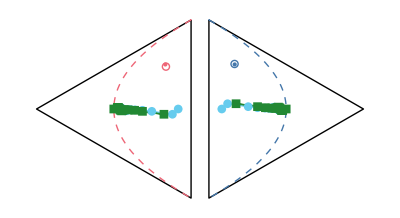

```mathematica
subrange=Round[Range[1,samples,samples/samples]];rplot[1]=ListPlot[{proj/@probh[[subrange,1]],proj/@mlprobh[[subrange,1]]},Axes->None,PlotRange->All,PlotStyle->{blue,green},Joined->True,PlotMarkers->Auto];
rplot[2]=ListPlot[{proj2/@probh[[subrange,2]],proj2/@mlprobh[[subrange,2]]},Axes->None,PlotRange->All,PlotStyle->{blue,green},Joined->True,PlotMarkers->Auto];

Show[{ddoms,plotfreqs@rfreqs[[1]],plotcfreqs@freqs[[1]],plotfreqs2@rfreqs[[2]],plotcfreqs2@freqs[[2]],rplot[1],rplot[2]},PlotRange->All]
```

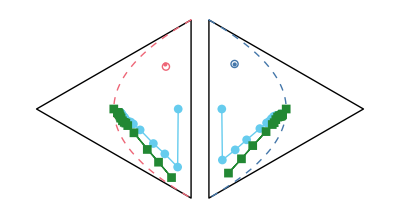

```mathematica
subrange=Round[Range[1,samples,samples/samples]];rplot[1]=ListPlot[{proj/@Exp[-logp[[subrange,1]]],proj/@Exp[-logmlp[[subrange,1]]]},Axes->None,PlotRange->All,PlotStyle->{blue,green},Joined->True,PlotMarkers->Auto];
rplot[2]=ListPlot[{proj2/@Exp[-logp[[subrange,2]]],proj2/@Exp[-logmlp[[subrange,2]]]},Axes->None,PlotRange->All,PlotStyle->{blue,green},Joined->True,PlotMarkers->Auto];

Show[{ddoms,plotfreqs@rfreqs[[1]],plotcfreqs@freqs[[1]],plotfreqs2@rfreqs[[2]],plotcfreqs2@freqs[[2]],rplot[1],rplot[2]},PlotRange->All]
```

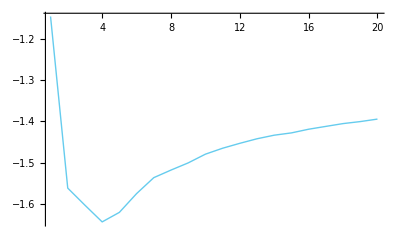

```mathematica
ListPlot[logev/Range[samples],Joined->True,PlotRange->All]
```

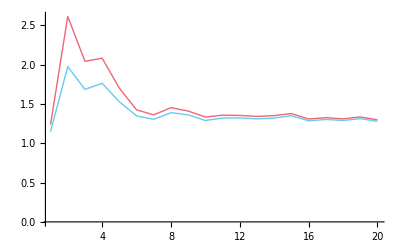

```mathematica
ListPlot[{logop,logomlp},Joined->True,PlotRange->All]
```

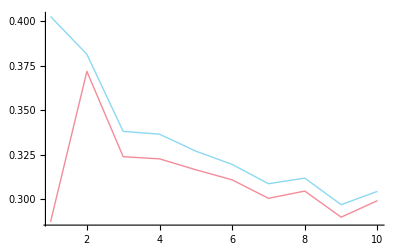

```mathematica
ListPlot[{oprob,omlprob},Joined->True,PlotStyle->Opacity[0.75],PlotRange->All]
```

```mathematica
entropy[p_]:=Block[{xlogx},
xlogx[x_]:=If[x>0,x*Log[x],0];
SetAttributes[xlogx,Listable];
Total@xlogx[p]];
```

```mathematica
(Exp@-entropy[rfreqs])^10*2//N
```

100218.

```mathematica
Log[Exp@-entropy[rfreqs],100000]//N
```

10.6385

```mathematica
rfreqs
```

{3/8,3/8,1/4}

```mathematica
(* cut *)
```

```mathematica
priort[t_,m_,s_]:=(PDF[NormalDistribution[m,s],t]+PDF[NormalDistribution[-m,s],t])/2;
```

```mathematica
priort[t_,m_,s_]:=(PDF[NormalDistribution[m,s],t]);
```

```mathematica
(* representation of parameter density on simplex *)
```

```mathematica
tran[t_]=FS[prob[t][[3]]]
```

1/(1+(2 Cosh[t])/11)

```mathematica
somax=prob[0][[3]]
```

11/13

```mathematica
dpdt[t_]=Assuming[Element[t,Reals],FullSimplify[Abs@D[tran[t],t]]]
```

(22 Abs[Sinh[t]])/(11+2 Cosh[t])^2

```mathematica
inve[so_]=t/.Flatten[Assuming[0<so<somax,FS@Solve[so==tran[t],t,Reals]]]
```

-ArcCosh[-(11 (-1+so))/(2 so)]

```mathematica
Plot[inve[so],{so,0,somax}]
```

```mathematica
dens[so_,mx_,sx_]=2*Assuming[0<so<somax,Simplify@priort[inve[so],mx,sx]/dpdt[inve[so]]]
```

((ⅇ^(-(mx-ArcCosh[-(11 (-1+so))/(2 so)])^2/(2 sx^2))+ⅇ^(-(mx+ArcCosh[-(11 (-1+so))/(2 so)])^2/(2 sx^2))) (11-(11 (-1+so))/so)^2)/(22 √(2 π) sx Abs[√((-1-(11 (-1+so))/(2 so))/(1-(11 (-1+so))/(2 so))) (1-(11 (-1+so))/(2 so))])

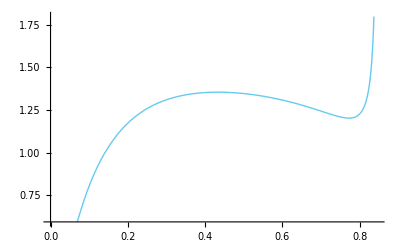

```mathematica
Plot[dens[so,2.5,1.2],{so,0,somax},PlotRange->Auto]
```

```mathematica
Limit[dens[so,6,1/2],so->somax]
```

∞

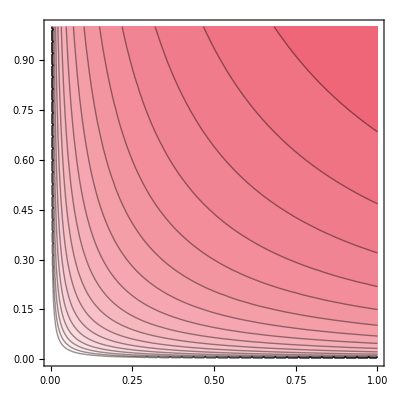

```mathematica
ContourPlot[Log[x*y],{x,0,1},{y,0,1},ColorFunction->mycolorfunction,Contours->20]
```

```mathematica
Table[{n,k},{n,3,5},{k,1,n}]
```

{{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3},{4,4}},{{5,1},{5,2},{5,3},{5,4},{5,5}}}

```mathematica
ttt=Flatten[ParallelTable[qq[k,n],{n,0.1,110,2.2},{k,0.1,2*n-0.1,2.1},Method->"CoarsestGrained"]];
```

```mathematica
Length@ttt
```

2594

```mathematica
tttr=Import["resub2.csv"];
```

```mathematica
Length@tttr
```

2594

```mathematica
Max[Abs[(ttt-tttr)/(ttt)]]
```

1.55864×10^-10

```mathematica
ttto=Import["resuo.csv"];
```

```mathematica
Length@ttto
```

2594

```mathematica
Max[Abs[(ttt-ttto)/(ttt)]]
```

2.53526×10^47

```mathematica
Limit[qq[k0+n*(2+xd),n0+2*n],n->+Infinity,Assumptions->0<k0<2*n0&&-2<xd<2]
```

Limit[-(Hypergeometric2F1[2 (2 n+n0),-k0+2 (2 n+n0)-n (2+xd),1-k0+2 (2 n+n0)-n (2+xd),-1]/(k0-2 (2 n+n0)+n (2+xd)))+Hypergeometric2F1[2 (2 n+n0),k0+n (2+xd),1+k0+n (2+xd),-1]/(k0+n (2+xd)),n→∞,Assumptions→0<k0<2 n0&&-2<xd<2]

```mathematica
lims[xd_,nt_,ng_]=Assuming[0<nt<ng&&-2<xd<2&&Element[xd,Integers]&&Element[nt,Integers]&&Element[ng,Integers],Simplify[-Log[Re[qq[(ng+nt)*(2+xd),2*(ng+nt)]/qq[nt*(2+xd),2*nt]]]/(2*(ng))]]
```

-1/(2 ng)Log[Re[(nt (-(2+xd) Hypergeometric2F1[4 (ng+nt),-(ng+nt) (-2+xd),1+4 (ng+nt)-(ng+nt) (2+xd),-1]+(-2+xd) Hypergeometric2F1[4 (ng+nt),(ng+nt) (2+xd),1+(ng+nt) (2+xd),-1]))/((ng+nt) (-(2+xd) Hypergeometric2F1[4 nt,-nt (-2+xd),1-nt (-2+xd),-1]+(-2+xd) Hypergeometric2F1[4 nt,nt (2+xd),1+nt (2+xd),-1]))]]

```mathematica
logq[k_,n_]=Assuming[0<k<2*n&&assu2,FS[Log[Re@qq[k,n]]]]
```

Log[(-1)^k Re[Beta[-1,k,1-2 n]+Beta[-1,-k+2 n,1-2 n]]]

```mathematica
logq[1000,1000]//N
```

-1388.48

```mathematica
lims[0,100.,1000.]//N
```

1.38689

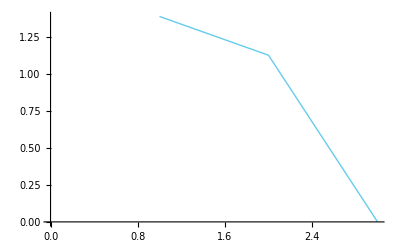

```mathematica
ListPlot[Table[lims[t,100.,1000.],{t,0,2}],Joined->True]
```

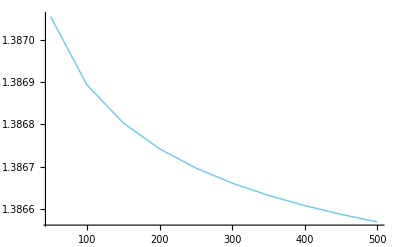

```mathematica
ListPlot[Table[{nt,lims[0,nt,1000]},{nt,50,500,50}],Joined->True,PlotRange->All]
```

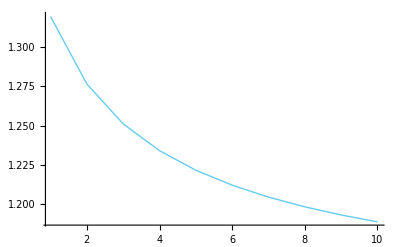

```mathematica
ListPlot[Table[{nt,lims[1,1,nt]},{nt,1,10,1}],Joined->True,PlotRange->All]
```

```mathematica
LogLinearPlot[lims[0,100,t],{t,100,10000}]
```

$Aborted

```mathematica
Limit[lims[xd,nt,ng],ng->+Infinity,Assumptions->(0<nt&&-2<xd<2)]
```

Limit[((-1)^(-(ng-nt) (2+xd)) ((-1)^(2 ng xd) Beta[-1,-ng (-2+xd),1-4 ng]+Beta[-1,ng (2+xd),1-4 ng]))/((-1)^(2 nt xd) Beta[-1,-nt (-2+xd),1-4 nt]+Beta[-1,nt (2+xd),1-4 nt]),ng→∞,Assumptions→0<nt&&-2<xd<2]

```mathematica
nnn=10^6;Plot3D[qq[0.1+nnn*(x1+2-x2),0.1+2*nnn],{x1,0,2},{x2,0,1},PlotPoints->10]
```

$Aborted

```mathematica
lims[xd_,nnx_:10^6]=Assuming[-2<xd<2&&nnx>0,FS[-Log[qq[0.1+nnx*(xd+2),0.1+2*nnx]/nnx]]]
```

-Log[1/nnx Re[1/(0.1+nnx (2+xd))Hypergeometric2F1[4. (0.05+nnx),0.1+nnx (2+xd),1.1+nnx (2+xd),-1]-(1. Hypergeometric2F1[0.2+4. nnx,0.1+nnx (2.-1. xd),1.1+nnx (2.-1. xd),-1])/(-0.1+nnx (-2.+xd))]]

```mathematica
lims[0,500]//N
```

1394.84

```mathematica
lims[0,10^3]//N
```

2782.17

```mathematica
lims[0,10^4]//N
```

$Aborted

```mathematica
nnn=10^6;qq[0.1+10^6*(x1+2-x2),0.1+2*nnn]
```

Re[-(Hypergeometric2F1[4.×10^6,4.×10^6-1000000 (2+x1-x2),4.×10^6-1000000 (2+x1-x2),-1]/(-4.×10^6+1000000 (2+x1-x2)))+Hypergeometric2F1[4.×10^6,0.1+1000000 (2+x1-x2),1.1+1000000 (2+x1-x2),-1]/(0.1+1000000 (2+x1-x2))]